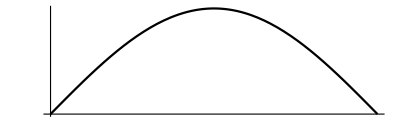

```mathematica
Plot[{Sin[x]},{x,0,Pi},AxesStyle->Arrowheads[0.04],Ticks->None,AspectRatio->1/Pi,PlotStyle->Black]
```

```mathematica
ParametricPlot3D[{x,Sin[x]*Cos[v],Sin[x]*Sin[v]},{v,0,2π},{x,0,π},Boxed->False,AxesStyle->Arrowheads[0.04],PlotPoints->25,MaxRecursion->5,Ticks->None,PlotStyle->Opacity[0.5]]
```

-Graphics3D-

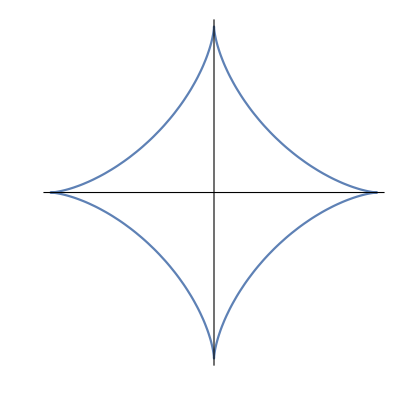

```mathematica
ParametricPlot[{(Cos[t])^3,(Sin[t])^3},{t,0,2Pi},AxesStyle->Arrowheads[0.04],Ticks->None]
```

```mathematica
RevolutionPlot3D[{(Cos[t])^3,(Sin[t])^3},{t,0,2Pi},Boxed->False,AxesStyle->Arrowheads[0.04],PlotPoints->25,MaxRecursion->5,Ticks->None,PlotStyle->Opacity[0.5]]
```

-Graphics3D-

```mathematica
FindMinimum[(1 + Cos[t])*Cos[t],{t,Pi/2}]
```

{-0.25,{t→2.0944}}

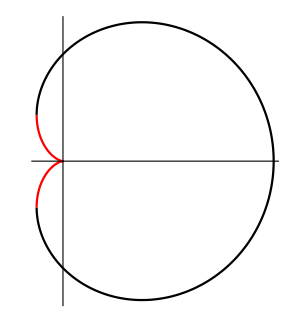

```mathematica
g1=ParametricPlot[{(1+Cos[t])*Cos[t],(1+Cos[t])*Sin[t]},{t,-2*Pi/3,2*Pi/3},AxesStyle->Arrowheads[0.04],Ticks->None,PlotStyle->Black];
g2=ParametricPlot[{(1+Cos[t])*Cos[t],(1+Cos[t])*Sin[t]},{t,2*Pi/3,4*Pi/3},AxesStyle->Arrowheads[0.04],Ticks->None,PlotStyle->Red];
Show[g1,g2]
```

```mathematica
RevolutionPlot3D[{(1+Cos[t-Pi/2])*Cos[t],(1+Cos[t-Pi/2])*Sin[t]},{t,0,2*Pi},PlotPoints->25,MaxRecursion->5,AxesStyle->Arrowheads[0.04],Ticks->None,PlotStyle->Opacity[0.5],Boxed->False]
```

-Graphics3D-

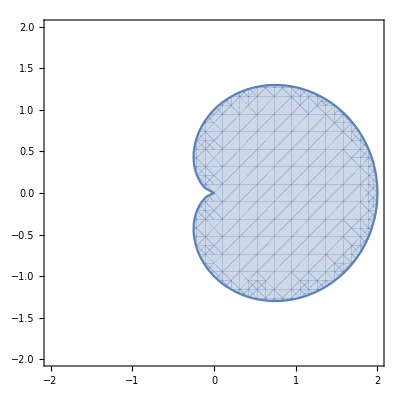

```mathematica
RegionPlot[Sqrt[x^2+y^2]-1-x/Sqrt[x^2+y^2]≤0,{x,-2,2},{y,-2,2}]
```

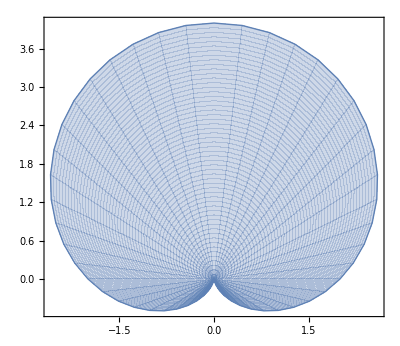

```mathematica
ParametricPlot[2 a (1+Cos[θ]) {Sin[θ],Cos[θ]},{a,0,1},{θ,-Pi,Pi},Mesh->False]
```

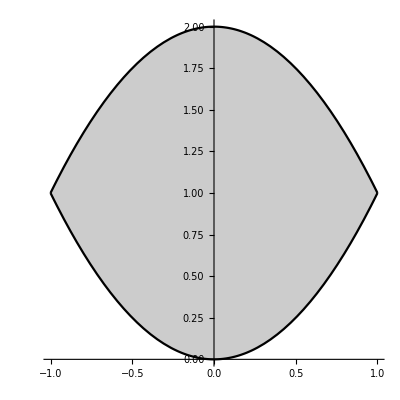

```mathematica
Plot[{x^2,2-x^2},{x,-1,1},AxesStyle->Arrowheads[0.04],Filling->{1->{2}},PlotStyle->Black,AspectRatio->1]
```

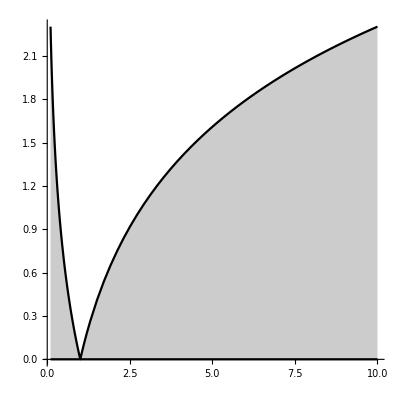

```mathematica
Plot[{Abs[Log[x]],0},{x,1/10,10},Filling->Bottom,AxesStyle->Arrowheads[0.04],GridLines->{{{1/10,Directive[Blue,Thick]},{10,Directive[Black,Thick]}},{}},PlotStyle->Black,AspectRatio->1]
```

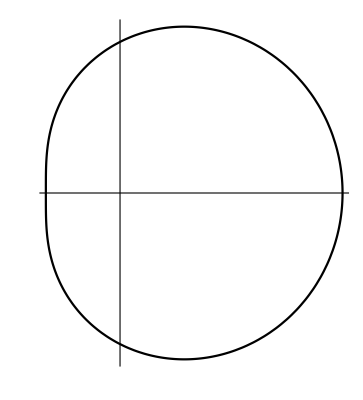

```mathematica
PolarPlot[1*Cos[t]+2,{t,0,2*Pi},AxesStyle->Arrowheads[0.04],Ticks->None,PlotStyle->Black]
```

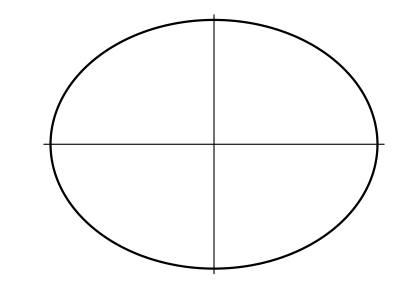

```mathematica
ParametricPlot[{4*Cos[t],3*Sin[t]},{t,0,2*Pi},AxesStyle->Arrowheads[0.04],Ticks->None,PlotStyle->Black]
```

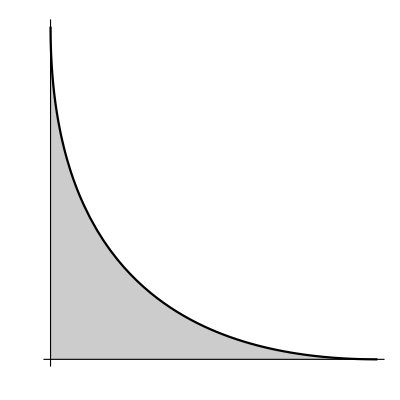

```mathematica
Plot[{4*(1-Sqrt[x/3])^2},{x,0,3},AxesStyle->Arrowheads[0.04],Filling->Bottom,Ticks->None,PlotStyle->Black,AspectRatio->1]
```

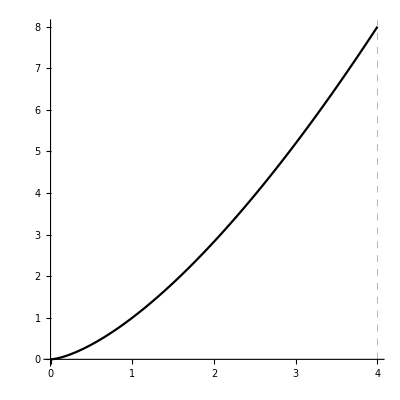

```mathematica
Plot[{x*Sqrt[x]},{x,0,4},AxesStyle->Arrowheads[0.04],GridLines->{{{4,Directive[Black,Dashed]}},{}},PlotStyle->Black,AspectRatio->1]
```

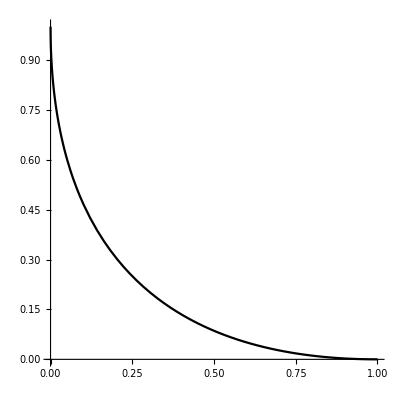

```mathematica
Plot[{(1-Sqrt[x])^2},{x,0,1},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1]
```

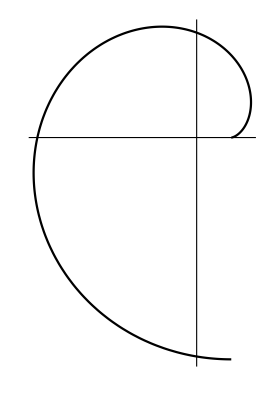

```mathematica
ParametricPlot[{Cos[t]+t*Sin[t],Sin[t]-t*Cos[t]},{t,0,2*Pi},AxesStyle->Arrowheads[0.04],Ticks->None,PlotStyle->Black]
```

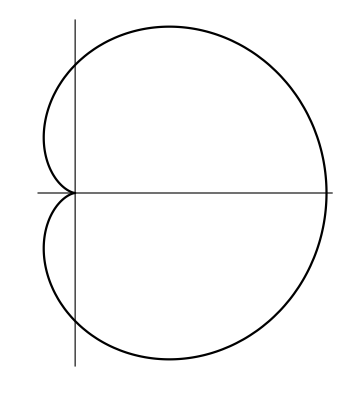

```mathematica
ParametricPlot[{(1+Cos[t])*Cos[t],(1+Cos[t])*Sin[t]},{t,0,2*Pi},AxesStyle->Arrowheads[0.04],PlotStyle->Black,Ticks->None]
```

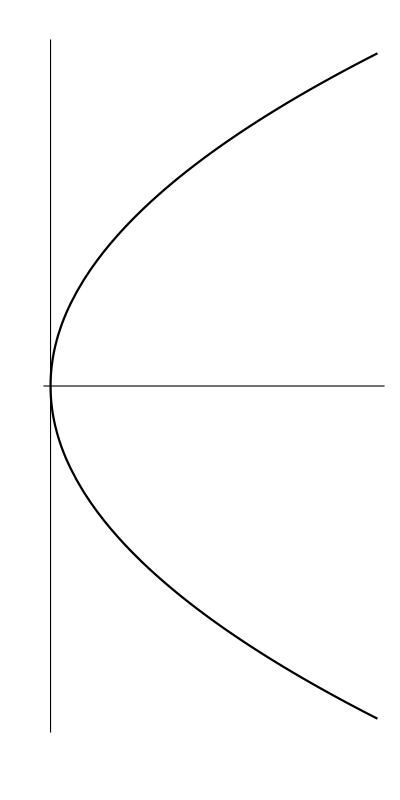

```mathematica
Plot[{Sqrt[2*x],-Sqrt[2*x]},{x,0,3},AxesStyle->Arrowheads[0.04],Ticks->None,PlotStyle->Black,AspectRatio->2]
```

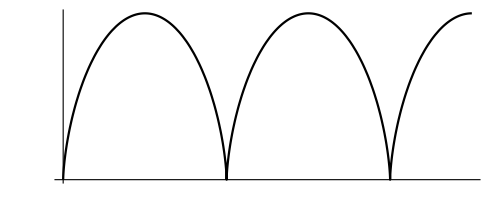

```mathematica
ParametricPlot[{t-Sin[t],1-Cos[t]},{t,0,5*Pi},AxesStyle->Arrowheads[0.04],Ticks->None,PlotStyle->Black]
```

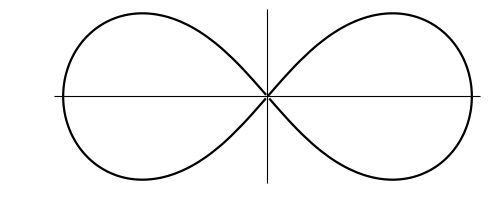

```mathematica
PolarPlot[{Sqrt[2*Cos[2*t]]},{t,0,2*Pi},AxesStyle->Arrowheads[0.04],Ticks->None,PlotStyle->Black]
```

```mathematica
Plot3D[{Sqrt[5^2*Sqrt[1-(x^2/3^2+y^2/4^2)]],-Sqrt[5^2*Sqrt[1-(x^2/3^2+y^2/4^2)]]},{x,-3,3},{y,-4,4},AxesStyle->Arrowheads[0.04],Ticks->None,PlotStyle->Automatic]
```

```mathematica
f[a_,b_,c_]:=ParametricPlot3D[{a*Sin[x1]Cos[x2],b*Sin[x1]Sin[x2],c*Cos[x1]},{x1,0,Pi},{x2,0,2 Pi}];
Table[{a,b,c}={Random[Real,{0,1}],Random[Real,{0,1}],Random[Real,{0,1}]};f[a,b,c],{i,1,10}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ParametricPlot3D[{5*Sin[x1]Cos[x2],3*Sin[x1]Sin[x2],4*Cos[x1]},{x1,0,Pi},{x2,0,2 Pi},Mesh->6,Ticks->None,BoundaryStyle->Black,AxesLabel->{x,y,z},PlotPoints->25,MaxRecursion->10,PlotStyle->Opacity[1]]
```

-Graphics3D-

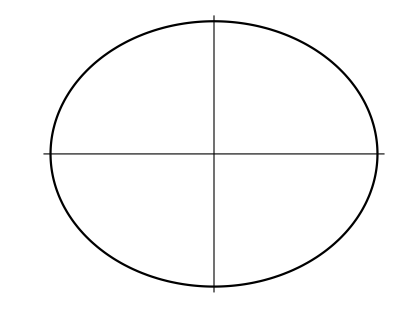

```mathematica
ParametricPlot[{5*Cos[t],4*Sin[t]},{t,0,2*Pi},AxesStyle->Arrowheads[0.04],Ticks->None,PlotStyle->Black]
```

```mathematica
ParametricPlot3D[{2Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]},{v,0,Pi},{u,0,2Pi},Mesh->5,BoundaryStyle->Black,PlotStyle->FaceForm[Red,Yellow]]
```

-Graphics3D-

```mathematica
g3=ParametricPlot3D[{Sin[x1]Cos[x2],Sin[x1]Sin[x2],Cos[x1]},{x1,0,Pi},{x2,0,2 Pi},Mesh->6,Ticks->None,BoundaryStyle->Black,AxesLabel->{x,y,z},PlotPoints->25,MaxRecursion->10,PlotStyle->{Opacity[0.5],FaceForm[Yellow]}];
g4=ParametricPlot3D[{1/2*Cos[t],1/2*Sin[t],z},{t,0,2*Pi},{z,-1,1},Mesh->6,Ticks->None,BoundaryStyle->Black,AxesLabel->{x,y,z},PlotPoints->25,MaxRecursion->10,PlotStyle->{Opacity[1],FaceForm[Blue]}];
Show[g3,g4]
```

-Graphics3D-

```mathematica
RegionPlot3D[x^2+y^2+z^2≤1&&x^2+y^2≤1/2,{x,-1,1},{y,-1,1},{z,-1,1},Mesh->30,Ticks->None,BoundaryStyle->Black,AxesLabel->{x,y,z},PlotPoints->25,MaxRecursion->10,PlotStyle->{Opacity[1],FaceForm[Red]}]
```

-Graphics3D-

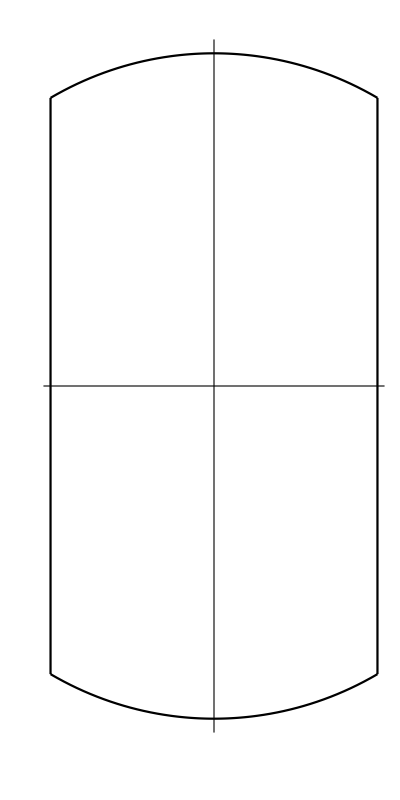

```mathematica
g5=Plot[{Sqrt[1-x^2],-Sqrt[1-x^2]},{x,-1/2,1/2},AxesStyle->Arrowheads[0.04],Ticks->None,PlotStyle->Black,AspectRatio->2];
g6=ParametricPlot[{1/2,y},{y,-Sqrt[3]/2,Sqrt[3]/2},AxesStyle->Arrowheads[0.04],Ticks->None,PlotStyle->Black];
g7=ParametricPlot[{-1/2,y},{y,-Sqrt[3]/2,Sqrt[3]/2},AxesStyle->Arrowheads[0.04],Ticks->None,PlotStyle->Black];
Show[g5,g6,g7]
```

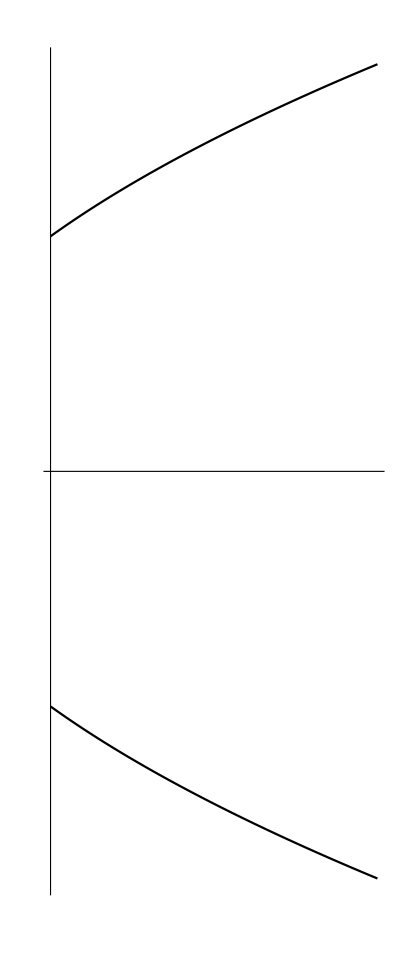

```mathematica
Plot[{Sqrt[2*x+2],-Sqrt[2*x+2]},{x,0,2},AxesStyle->Arrowheads[0.04],Ticks->None,PlotStyle->Black,AspectRatio->Sqrt[6]]
```

```mathematica
ParametricPlot3D[{x,(Sqrt[2*x+2])*Cos[v],(Sqrt[2*x+2])*Sin[v]},{v,0,2π},{x,0,2},Boxed->False,AxesStyle->Arrowheads[0.04],PlotPoints->25,MaxRecursion->5,Ticks->None,PlotStyle->Opacity[0.5]]
```

-Graphics3D-

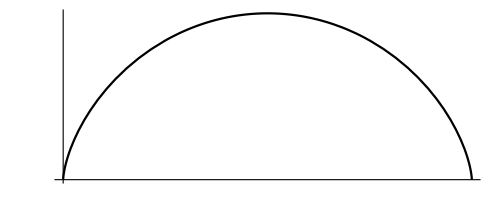

```mathematica
ParametricPlot[{t-Sin[t],1-Cos[t]},{t,0,2*Pi},AxesStyle->Arrowheads[0.04],Ticks->None,PlotStyle->Black]
```

```mathematica
ParametricPlot3D[{t-Sin[t],(1-Cos[t])*Cos[v],(1-Cos[t])*Sin[v]},{v,0,2π},{t,0,2π},Boxed->False,AxesStyle->Arrowheads[0.04],PlotPoints->25,MaxRecursion->5,Ticks->None,PlotStyle->Opacity[0.5]]
```

-Graphics3D-